```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/m0/m0_500/midmub

```mathematica
chi0=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi0.dat"]],{i,800,960,5}];
chi1=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi1.dat"]],{i,800,960,5}];
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,800,960,5}];
chi3=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi3.dat"]],{i,800,960,5}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,800,960,5}];
r42=chi4/chi2//Quiet;
(*r21=chi2/chi1//Quiet;
r12=chi1/chi2//Quiet;
r32=chi3/chi2//Quiet;
r31=chi3/chi1//Quiet;*)
```

```mathematica
(*r42[[1;;45]][[1;;60]]=1;
r42[[46;;55]][[1;;50]]=1;
r42[[56;;62]][[1;;40]]=1;
r42[[63;;78]][[1;;20]]=1;
r42[[79;;80]][[1;;15]]=1;*)
(*r42[[85;;88]][[1;;10]]=1;*)
```

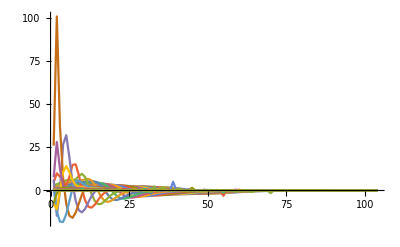

```mathematica
ListLinePlot[Table[r42[[i]],{i,1,33}],PlotRange->{All,All}]
```

```mathematica
mub=Table[i,{i,800,960,5}];
T=Table[i,{i,1,120,1}];
```

```mathematica
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],If[i<17,0,r42[[j]][[i-16]]]},{i,1,120},{j,1,33}],1];
Export["r42mid.dat",R42all]
```

r42mid.dat

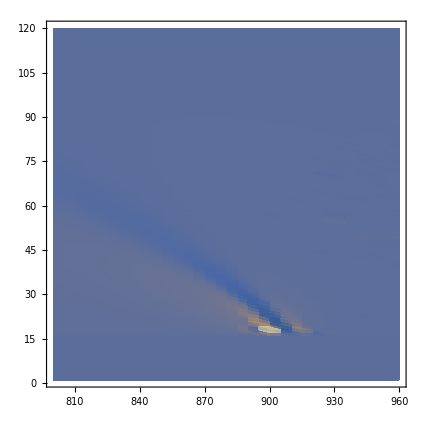

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-100,100}}]
```